基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","snslib.wl"}])
```

WorkPath :

```mathematica
SetDirectory["D:\\Work\\SSR\\basePlan"];
dataPath = FileNameJoin[{ParentDirectory[],"_data"}]
```

D:\Work\SSR\_data

```mathematica
Config :
```

```mathematica
ClearAll[params,soliderConfig,heroConfig,dayByHeroLv];
params = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"battle","param"];
soliderConfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"solider","base"];
heroConfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"hero","hero"];
dayByHeroLv = Import["D:\\Work\\SSR\\_data\\dayByheroLv.txt","Table"]//Flatten;
```

```mathematica
战斗公式：
```

普攻伤害 = k *^n √兵力  * b * 兵种攻击 * 主将力/智  *  (1- · /(主将耐/智 * 兵种防+a)) /兵种血

```mathematica
ClearAll[slgDamage];
slgDamage[num_,atk_,def_,herolv_] := params[First,"num_k"] * num^(1/params[First,"num_n"]) * params[First,"dam_b"] *atk * (1- def/(def+params[herolv,"def_a"]));
defValue[herolv_]:= 1/params[IntegerPart@herolv,"def_a"];
```

## 上阵兵力

标准兵力 (单队出征容量) = 主堡容量 + 列阵广场容量  + 英雄容量

```mathematica
ClearAll[soliderNum,mainData,armyData,heroData];
soliderNum[lv_]:= 500 + 250 * lv^2;
soliderNum[lv_,key_String]:= Round[Base`excleLookUp[soliderConfig,"Lv"->lv,key]*soliderNum[lv],100];
armyData = Association@@Table["attr_building_army_"<>ToString[n]-><|"数值1"->soliderNum[n,"build"]|>,{n,1,maxLv}];
mainData = Association@@Table["attr_building_base_"<>ToString[n]-><|"数值1"->soliderNum[n,"main"]|>,{n,1,maxLv}];
heroData = Association@@Table["attr_hero_"<>ToLowerCase[rank]<>"_lv"<>ToString[n]-><|"数值0"->soliderNum[Base`excleInterpolation[lvconfig,"heroLv"->n,"Lv"],"hero"]*Base`excleLookUp[heroConfig,"rank"->rank,"solider"]|>,{n,1,lvconfig[Last,"heroLv"]},{rank,{"S","A","B","C"}}];
```

```mathematica
snsExportTable["attrgroup-build.csv",snsUpdateTable["attrgroup-build",Merge[{armyData,mainData},First]]]
```

C:\k-config\excel\attrgroup-build.csv

```mathematica
snsExportTable["attrgroup-hero.csv",snsUpdateTable["attrgroup-hero",heroData]]
```

C:\k-config\excel\attrgroup-hero.csv

## 战斗时间

战斗时间(回合数) = 标准兵力/标准伤害  ->  基础攻击 = 兵种血*兵力^(1-1/n)/(战斗时间*k*b)

```mathematica
ClearAll[battleConfig,soliderHp,battleTime,soliderAttrConfig,baseAtk];
battleConfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"battle","base"];
soliderAttrConfig := Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"solider","attr"];
soliderHp[lv_]:= Base`excleLookUp[soliderAttrConfig,"Lv"->lv,"st_hp"];
battleTime[herolv_] := Base`excleInterpolation[battleConfig,"herolv"->herolv,"battleTime"];
baseAtk[herolv_]:= Module[{lv=Base`excleInterpolation[lvconfig,"heroLv"->herolv,"Lv"]},soliderHp[lv]*soliderNum[lv]^(1-1/params[First,"num_n"])/(battleTime[herolv]* params[First,"num_k"] * params[First,"dam_b"])];
```

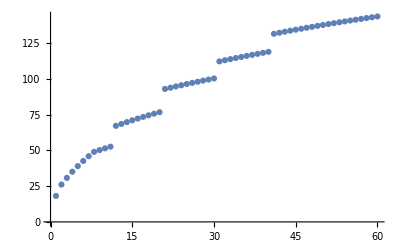

```mathematica
ListPlot@Table[baseAtk[n],{n,1,lvconfig[Last,"heroLv"]}]
```

```mathematica
test[herolv_,def_]:=Module[{lv=Base`excleInterpolation[lvconfig,"heroLv"->herolv,"Lv"]},soliderNum[lv]*soliderHp[lv]/slgDamage[soliderNum[lv],baseAtk[herolv]*(def*defValue[herolv]+1),def,herolv]];
Table[Round[battleTime[n]-test[n,1],0.01],{n,1,lvconfig[Last,"heroLv"]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## 基础攻击

putAtk =  baseAtk *(putDef*defValue+1)

```mathematica
ClearAll[soliderAttack];
soliderAttack = (baseAtk[Base`excleInterpolation[lvconfig,"Lv"->#,"heroLv"]]*(Base`excleLookUp[soliderAttrConfig,"Lv"->#,"st_def"]*defValue[Base`excleInterpolation[lvconfig,"Lv"->#,"heroLv"]]+1)&)/@(Normal@soliderAttrConfig[All,"Lv"])
```

{36.3424,84.9041,116.346,146.516,167.365,188.975}

```mathematica
Normal@soliderAttrConfig[All,"Lv"]
```

{1.,10.,15.,20.,25.,30.}

```mathematica
defValue[10.0]
```

0.00526316

## 产出数据

```mathematica
ClearAll[resData,resGetByLv];
resData[id_,lv_]:= Module[{x},<|"lv"->lv,"base"->1/resValue[id,lv],"productBase"-> resProductBase[id,lv],"bdNum"->bdNum[id,lv],"productStudy"-> advanceParams[id,"study"]*(lv-1),"productHero"-> advanceParams[id,"hero"]*(lv-1),"productVip"-> advanceParams[id,"vip"]*(lv-1),"productHours"->productHours[[lv]],"collectBase"->collectBaseParams[id]*(lv-1),"troopNum"->troopNum[lv],"resNum"-> resNum[lv],"collectStudy"-> collectAdvanceParams[id,"study"]*(lv-1),"collectHero"-> collectAdvanceParams[id,"hero"]*(lv-1),"collectVip"-> collectAdvanceParams[id,"vip"]*(lv-1),"collectHours"-> collectHours[lv],"other"-> Base`excleLookUp[otherconfig,"lv"-> lv,id]*productHours[[lv]]/resValue[id,lv]|>];
resGetByLv[id_,lv_]:= Module[{data=Dataset@resData[id,lv]},<|"product"->data[#productBase*#bdNum*(1+#productStudy+#productHero+#productVip)*#productHours&],"collect"->data[#collectBase*troopNum[lv]/resNum[lv]*(1+#collectStudy+#collectHero+#collectVip)*#collectHours&],"other"->data["other"]|>];
```

```mathematica
Export[FileNameJoin[{dataPath,#<>"_"<>"resData.txt"}],Table[resData[#,n],{n,1,maxLv}]//Dataset,"Table"]&/@resconfig[All,"id"];
```

<|product→3.01104×10^7,collect→2.69884×10^7,other→2.25429×10^7|>

## 消耗

消耗/产出 分段函数(波折)：

```mathematica
ClearAll[funcsAccumulate,resConsumeByLv,consumeData];
funcsAccumulate = Table[Fit[Normal/@Values/@{consumeconfig[n,{"lv","accumulate"}],consumeconfig[n+1,{"lv","accumulate"}]},{1,x,x^consumeconfig[n,"power"]},x],{n,1,Length@consumeconfig-1}];
funcsAccumulate = PrependTo[funcsAccumulate,x];
accumulateByLv[lv_]:= funcsAccumulate[[Base`excleIndex[consumeconfig,"lv"-> lv]]]/.x->lv;
resConsumeByLv[id_,lv_]:=Total[resGetByLv[id,lv]]/accumulateByLv[lv];
consumeData[res_String,lv_]:=Module[{base=resConsumeByLv[res,lv],config=Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource",res]},<|"lv"-> lv,"base"-> base,(#->base*Base`excleLookUp[{consumeconfig,"lv"-> lv},{config,#}])&/@Normal[config[First,Keys]]|>];
```

```mathematica
Export[FileNameJoin[{dataPath,#<>"_"<>"consumeData.txt"}],Table[consumeData[#,n],{n,1,maxLv}]//Dataset,"Table"]&/@resconfig[All,"id"];
```

```mathematica
consumeData["r4",10]
```

<|lv→10,base→4388.68,equip→3291.51,studyE→438.868,studyM→438.868,army→219.434|>